Steady-State Binary Fickian Diffusion

```mathematica
Manipulate[
Module[{Dab,Cm,A1,B1,C1,VP,VPhot,Jdiff,Jtot,yCold,yA0,yAL,yConv,L2,p1,p2},
 Dab=( 1.17*10^-9)*(T+273)^(3/2)/Ptot;(*cm^2/s*)
Cm=Ptot/((8.20567*10^-5)*(T+273));(*mol/m^3*)

A1=6.90940;B1=1349.820;C1=209.385;
VP=1/760*10^(A1-B1/(T+C1));(*using antoine eq to get VP in atm*)
VPhot=1/760*10^(A1-B1/(T+C1));

Jdiff=(Cm*Dab*VP)/(L*Ptot);(*Diffusive flux mol/m^2/s*)
Jtot=Dab*Cm/L*Log[1/(1-(VP/Ptot))];
yCold[z_]:=-(VP*z)/(L*Ptot)+VP/Ptot;

yA0=VPhot/Ptot;
yAL=0;(*boundry Condition*)
yConv[z_]:=1-((1-yAL)/(1-yA0))^(z/L)*(1-yA0);

L2=0.5*(1+Rescale[L,{0,120}]);(*height of vapor, not sure if right. Rescale rescales range from 0 to 1*)

p1=Plot[If[Jdiff/Jtot > 0.9,yCold[z],yConv[z]],{z,0,L},PlotStyle->{Thick,If[Jdiff/Jtot > 0.9,Black,Blue]}, PlotRange->{{0,L},{0,1}},Frame->True,FrameTicks->True,FrameLabel->{"height (cm)","octane mole fraction"},LabelStyle->{17,Black},ImageSize->{300,400},AspectRatio->Full,ImagePadding->{{50,15},{50,10}},
Epilog->Text[Style[Column[{"convective flux",If[Jdiff/Jtot > 0.9,"insignificant (<10%)","significant (>10%)"]},Center],17],{0.5*L,0.85}]];


p2=Graphics3D[{
{LightBlue,Cylinder[{{0,0,0},{0,0,0.15}},0.3]},
{Opacity[0.2+0.8*Rescale[If[Jdiff/Jtot > 0.9,yCold[0],yConv[0]],{0.004645,0.8523}],RGBColor[0,0.6,0]],Cylinder[{{0,0,0.15},{0,0,L2}},0.3]},
{Arrowheads@Large,Arrow[{{-0.3,0,L2+#},{0.3,0,L2+#}}]&/@{0.1,0.15,0.2}},

Text[Framed[Style[Row@{Subscript[Style["y",Italic],Row@{Style["z",Italic],"=0"}]," = ",NumberForm[If[Jdiff/Jtot > 0.9,yCold[0],yConv[0]],2]},17]],{0.25,0,0.15},{-3,0}],
(*Text[Style[Column[{
Row@{"flux ",""["mol"/Row@{Superscript["m",2]," s"}]},
Framed@Column[{Row@{"convective = ",NumberForm[Jtot-Jdiff,{2,1}]},Row@{"diffusive = ",NumberForm[Jdiff,{2,1}]}},Alignment->"="]
},Center],17],{0.25,0,0.5},{-1.2,0}],*)
Text[Style[Column[{
Row@{"flux ",""["nmol"/Row@{Superscript["cm",2]," s"}]},
Framed@Column[{Row@{"convective = ",ScientificForm[(Jtot-Jdiff)*(1*^9)/1000^2,2]},Row@{"diffusive = ",ScientificForm[Jdiff*(1*^9)/1000^2,2]}},Alignment->"="]
},Center],17],{0.25,0,0.5},{-1.2,0}],

Text[Style[Column[{"octane","liquid"},Center],17,Background->None],{0.03,-0.3,0.07}],
Text[Style[Row@{Style["z",Italic]," = 0 cm"},17],{0.25,0,0.15},{-1.5,0}],
Text[Style[Row@{Style["z",Italic]," = ",L," cm"},17],{0.25,0,L2},{-1.5,0}]
},Boxed->False,ViewPoint->Front,ImageSize->{300,400},AspectRatio->Full,PlotRange->{{-0.3,1.7},All,{0,1.25}}];


Grid@{{p1,p2}}
],
Grid[{
{Control[{{Ptot,1,"total pressure (atm)"},1,3,0.3,Appearance->"Labeled",ImageSize->Small}],
Control[{{L,120,"tube height (cm)"},45,120,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{T,90,"system temperature (°C)"},20,120,1,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```

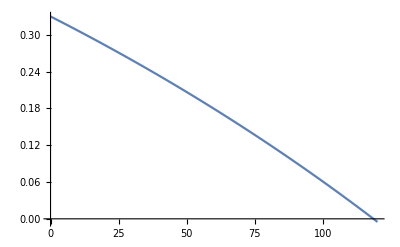

```mathematica
Module[{y},
y[x_]:=1-0.67*1.5^(x/120);

Plot[y[x],{x,0,120}]
]
```

```mathematica
Manipulate[
Module[{Dab,Cm,A1,B1,C1,VP,VPhot,Jdiff,Jtot,yCold,yA0,yAL,yConv,L2,p1,p2},
 Dab=( 1.17*10^-9)*(T+273)^(3/2)/Ptot;(*cm^2/s*)
Cm=Ptot/((8.20567*10^-5)*(T+273));(*mol/m^3*)

A1=6.90940;B1=1349.820;C1=209.385;
VP=1/760*10^(A1-B1/(T+C1));(*using antoine eq to get VP in atm*)
VPhot=1/760*10^(A1-B1/(T+C1));

Jdiff=(Cm*Dab*VP)/(L*Ptot);(*Diffusive flux mol/m^2/s*)
Jtot=Dab*Cm/L*Log[1/(1-(VP/Ptot))];
yCold[z_]:=-(VP*z)/(L*Ptot)+VP/Ptot;

yA0=VPhot/Ptot;
yAL=0;(*boundry Condition*)
yConv[z_]:=1-((1-yAL)/(1-yA0))^(z/L)*(1-yA0);

L2=0.5*(1+Rescale[L,{0,120}]);(*height of vapor, not sure if right. Rescale rescales range from 0 to 1*)


ParametricPlot3D[{Cos[u],Sin[u],2v},{u,0,2Pi},{v,0,L2},ColorFunction->(Opacity[0.2+0.8*Rescale[If[Jdiff/Jtot > 0.9,yCold[#],yConv[#]],{0.004645,0.8523}],RGBColor[0,0.6,0]]&),ColorFunctionScaling->False,BoundaryStyle->Black,Mesh->None]
],
Grid[{
{Control[{{Ptot,1,"total pressure (atm)"},1,3,0.3,Appearance->"Labeled",ImageSize->Small}],
Control[{{L,120,"tube height (cm)"},45,120,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{T,90,"system temperature (°C)"},20,120,1,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```

This Demonstration illustrates the concentration profile and the flux in steady-state diffusion. Pure liquid octane is at the bottom of the long vertical tube, above the liquid is a quiescent layer of air. At the open end on top, air is blown to sweep the octane vapor making it's concentration at the top equal to zero. Use sliders to change the total pressure, height of the tube, and temperature. The color of the curve changes colors to blue to indicate that convective flux is significant.





The diffusive flux and total flux are:

J_diff=(C_m D_AB P^sat)/(L P),

J_tot=D_AB C_m/L ln (1/(1-P^sat/P)),

where J_diff is the diffusive flux (mol/[m^2 s]), J_tot is the total flux  (mol/[m^2 s]), C_m is molar concentration (mol/m^3), D_AB is the diffusivity (cm^2/s), P^sat is vapor pressure (atm), L is the tube height (m), and P is total pressure (atm).

The vapor pressure is calculated using the Antoine equation:

P^sat=10^(A-B/(T+C)),

where A, B, and C are Antoine constants, and T is temperature (°C).

If the diffusive flux dominates (greater than 90% of the total flux), we assume that the convective flux is zero, the concentration profile is:

y=-(z P^sat)/(L P)+P^sat/P,

where y is mole fraction, and z is tube height (m).

When the convective flux dominates (greater than 10% of the total flux), the concentration profile is:

y=1-((1-y_(A,L))/(1-y_(A,0)))^(z/L) (1-y_(A,0)),

where y_(A,L) is the mole fraction at z=L, and y_(A,0) is the mole fraction at z=0.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

chemical engineering

diffusion

Fickian diffusion

steady-state

Contributed by: Muqbil Alkhalaf and Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)